```mathematica
Plot3D[Re[1/(a^2+b^2)*a-1/(a^2+b^2)*b*ⅈ],{a,-10,10},{b,-10,10}]
Plot3D[Im[1/(a^2+b^2)*a-1/(a^2+b^2)*b*ⅈ],{a,-10,10},{b,-10,10}]
```

-Graphics3D-

-Graphics3D-

```mathematica
Plot3D[a/(a^2+b^2)-b/(a^2+b^2),{a,-10,10},{b,-10,10}]
```

-Graphics3D-

```mathematica
testTable=Table[{x^2,y^2},{x,-5,5},{y,-5,5}]
```

{{{25,25},{25,16},{25,9},{25,4},{25,1},{25,0},{25,1},{25,4},{25,9},{25,16},{25,25}},{{16,25},{16,16},{16,9},{16,4},{16,1},{16,0},{16,1},{16,4},{16,9},{16,16},{16,25}},{{9,25},{9,16},{9,9},{9,4},{9,1},{9,0},{9,1},{9,4},{9,9},{9,16},{9,25}},{{4,25},{4,16},{4,9},{4,4},{4,1},{4,0},{4,1},{4,4},{4,9},{4,16},{4,25}},{{1,25},{1,16},{1,9},{1,4},{1,1},{1,0},{1,1},{1,4},{1,9},{1,16},{1,25}},{{0,25},{0,16},{0,9},{0,4},{0,1},{0,0},{0,1},{0,4},{0,9},{0,16},{0,25}},{{1,25},{1,16},{1,9},{1,4},{1,1},{1,0},{1,1},{1,4},{1,9},{1,16},{1,25}},{{4,25},{4,16},{4,9},{4,4},{4,1},{4,0},{4,1},{4,4},{4,9},{4,16},{4,25}},{{9,25},{9,16},{9,9},{9,4},{9,1},{9,0},{9,1},{9,4},{9,9},{9,16},{9,25}},{{16,25},{16,16},{16,9},{16,4},{16,1},{16,0},{16,1},{16,4},{16,9},{16,16},{16,25}},{{25,25},{25,16},{25,9},{25,4},{25,1},{25,0},{25,1},{25,4},{25,9},{25,16},{25,25}}}

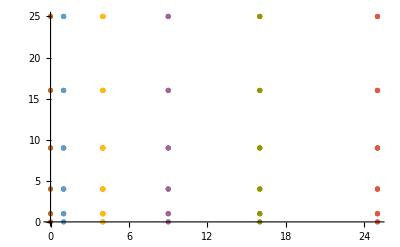

```mathematica
ListPlot@testTable
```

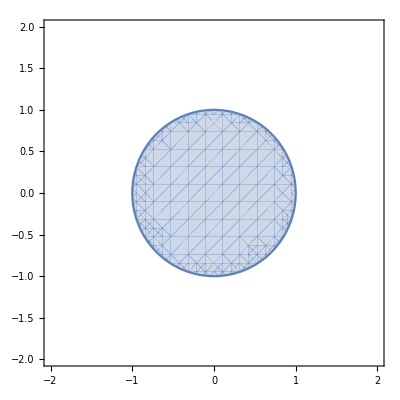

```mathematica
circle=RegionPlot[x^2+y^2<1,{x,-2,2},{y,-2,2}]
```

```mathematica
nthRootsOfUnity[n_]:=Table[Cos[k*2*π]/n,Sin[k*2*π]/n,{k,0,n}]
```

```mathematica
nthRootsOfUnity[3]
```

{1/3,Cos[360]/3+1/3 ⅈ Sin[360],Cos[720]/3+1/3 ⅈ Sin[720],Cos[1080]/3+1/3 ⅈ Sin[1080]}

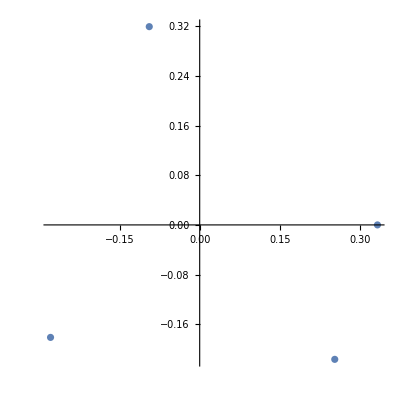

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{1/3,Cos[360]/3+1/3 ⅈ Sin[360],Cos[720]/3+1/3 ⅈ Sin[720],Cos[1080]/3+1/3 ⅈ Sin[1080]},AspectRatio->1]
```

```mathematica
{1/3,Cos[360]/3+1/3 ⅈ Sin[360],Cos[720]/3+1/3 ⅈ Sin[720],Cos[1080]/3+1/3 ⅈ Sin[1080]}
```

{1/3,Cos[360]/3+1/3 ⅈ Sin[360],Cos[720]/3+1/3 ⅈ Sin[720],Cos[1080]/3+1/3 ⅈ Sin[1080]}

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{1/3,Cos[360]/3+1/3 ⅈ Sin[360],Cos[720]/3+1/3 ⅈ Sin[720],Cos[1080]/3+1/3 ⅈ Sin[1080]},AspectRatio->1]
```

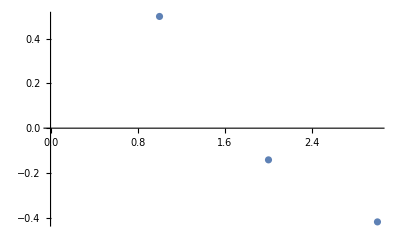

```mathematica
ListPlot[nthRootsOfUnity[1]]
```

```mathematica
circle=RegionPlot[x^2+y^2<1,{x,-2,2},{y,-2,2}]
```

-Graphics-

```mathematica
points[N_]:=Table[Table[ {Cos[k*2*360/n Degree],Sin[k*2*360/n Degree]},{k,0,n}],{n,0,N}]
```

```mathematica
pointsn[a_]:= Table[ {Cos[k*2*360/a Degree],Sin[k*2*360/a Degree]},{k,0,a}]
```

SetDelayed::write: Tag List in {{1,0},{-1/2,-(√3)/2},{-1/2,(√3)/2},{1,0}}[a_] is Protected.

$Failed

```mathematica
pointsn[8]
```

{{1,0},{-1/2,-(√3)/2},{-1/2,(√3)/2},{1,0}}[8]

Table::nliter: Non-list iterator 1/3 Sin[k 2 π] at position 2 does not evaluate to a real numeric value.

Table[1/3 Cos[k 2 π],1/3 Sin[k 2 π],{k,0,3}]

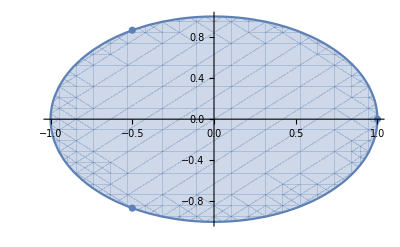

```mathematica
Show[{points,circle},PlotRange->All]
```

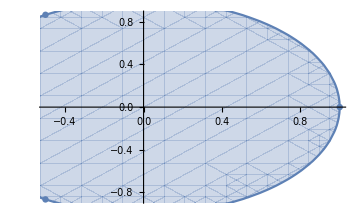

```mathematica
Show[%44,ImageSize->Medium]
```

```mathematica
For[i=1;t=x,i^2<10,i++,t=t^2+i;Print[t]]
For
```

```mathematica
For[i=0,i<5,i++,i<5;ListPlot[Table[ {Cos[k*2*360/i Degree],Sin[k*2*360/i Degree]},{k,0,i-1}]]]
```

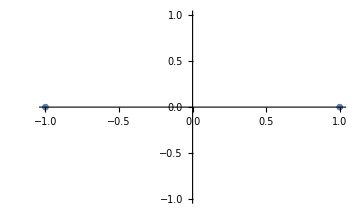

```mathematica
Show[%33,ImageSize->Medium]
```

```mathematica
MatrixForm[foo]
```

Null

```mathematica
ListPlot[foo]
```

ListPlot::lpn: Null is not a list of numbers or pairs of numbers.

ListPlot[Null]

```mathematica
Transpose[{{1,0},{-1,0},{1,0},{-1,0}}]
```

{{1,-1,1,-1},{0,0,0,0}}

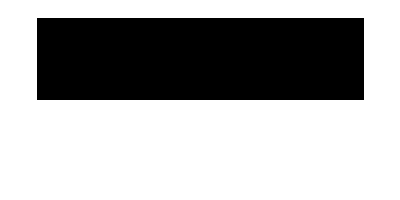

```mathematica
ArrayPlot[{{1,-1,1,-1},{0,0,0,0}}]
```

```mathematica
MatrixForm[{{1,0},{-1,0},{1,0},{-1,0}}]
```

(1 | 0
-1 | 0
1 | 0
-1 | 0)

```mathematica
Grid[{{1,0},{-1,0},{1,0},{-1,0}}]
```

1 | 0
-1 | 0
1 | 0
-1 | 0

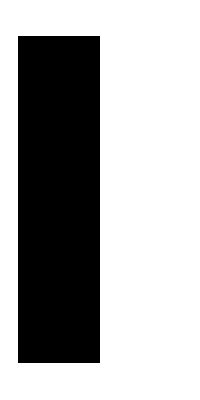

```mathematica
ArrayPlot[First[Grid[{{1,0},{-1,0},{1,0},{-1,0}}]]]
```

```mathematica
TableForm[{{1,0},{-1,0},{1,0},{-1,0}}]
```

1 | 0
-1 | 0
1 | 0
-1 | 0

```mathematica
Transpose[{{1,0},{-1/2,-(√3)/2},{-1/2,(√3)/2}}]
```

{{1,-1/2,-1/2},{0,-(√3)/2,(√3)/2}}

```mathematica
TableForm[{{1,-1/2,-1/2},{0,-(√3)/2,(√3)/2}}]
```

1 | -1/2 | -1/2
0 | -(√3)/2 | (√3)/2

```mathematica
TableForm[{{1,0},{-1/2,-(√3)/2},{-1/2,(√3)/2}}]
```

1 | 0
-1/2 | -(√3)/2
-1/2 | (√3)/2

```mathematica
TableForm[{{1,0},{-1/2,-(√3)/2},{-1/2,(√3)/2},{1,0}}]
```

1 | 0
-1/2 | -(√3)/2
-1/2 | (√3)/2
1 | 0